# Higgs to two photon

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.8

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 1 Jul 13

FormCalc 8.2

by Thomas Hahn

last revised 2 Jul 13

### h → γ γ Matrix Element Calculation

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.8/Models/SM.mod

> 43 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 114 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 22 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

Restoring 18 field point(s)

in total: 28 Particles insertions

> Top. 1: 22 diagrams

> Top. 2: 2 diagrams

> Top. 3: 2 diagrams

> Top. 4: 2 diagrams

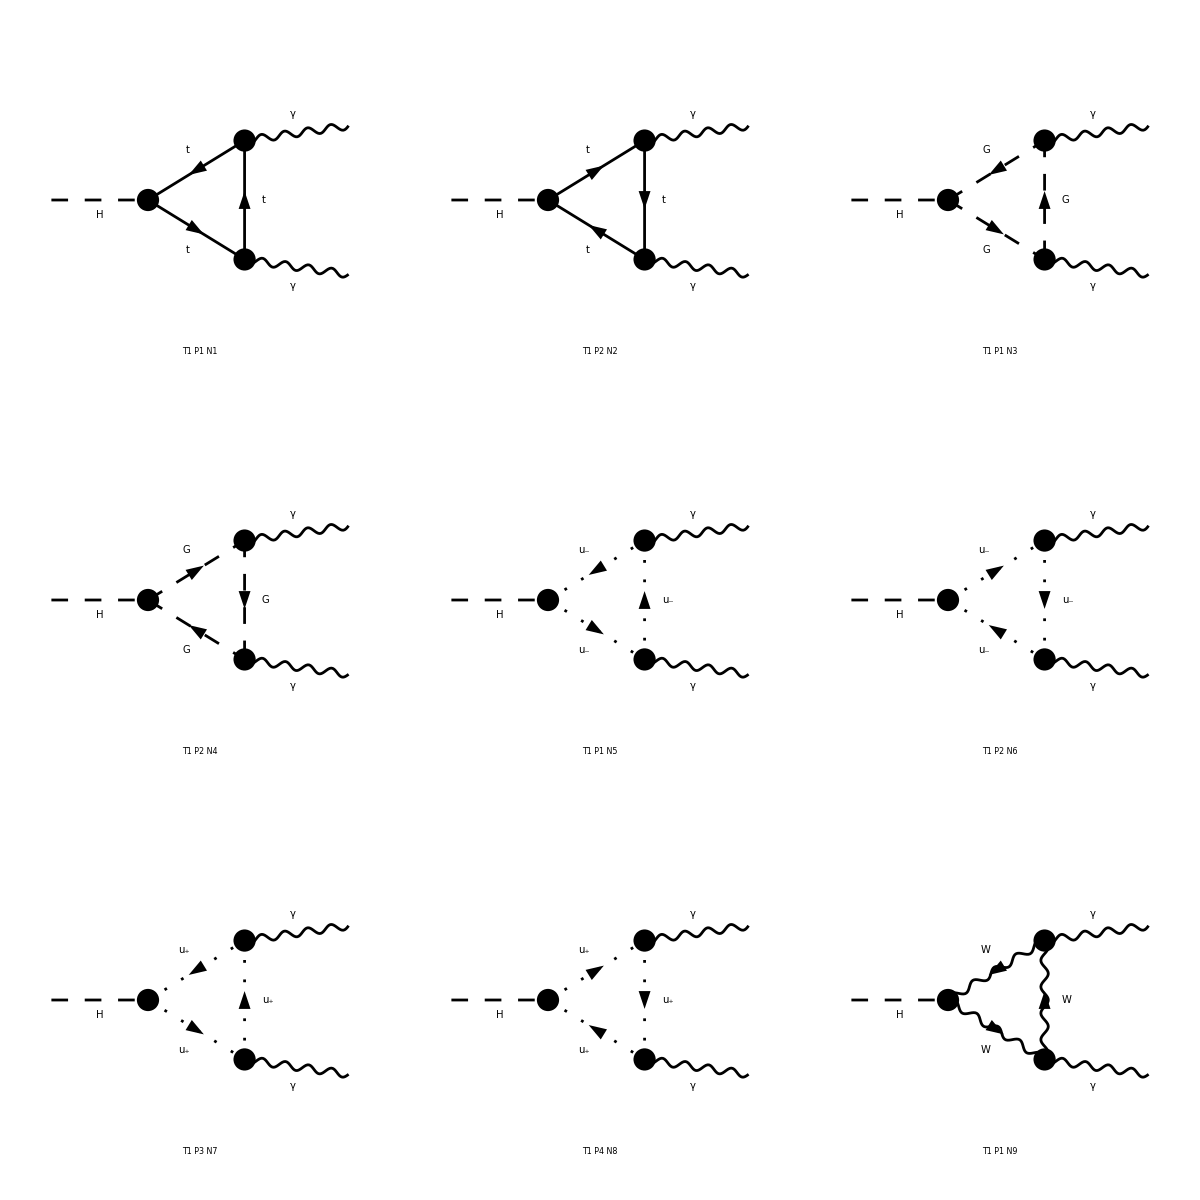

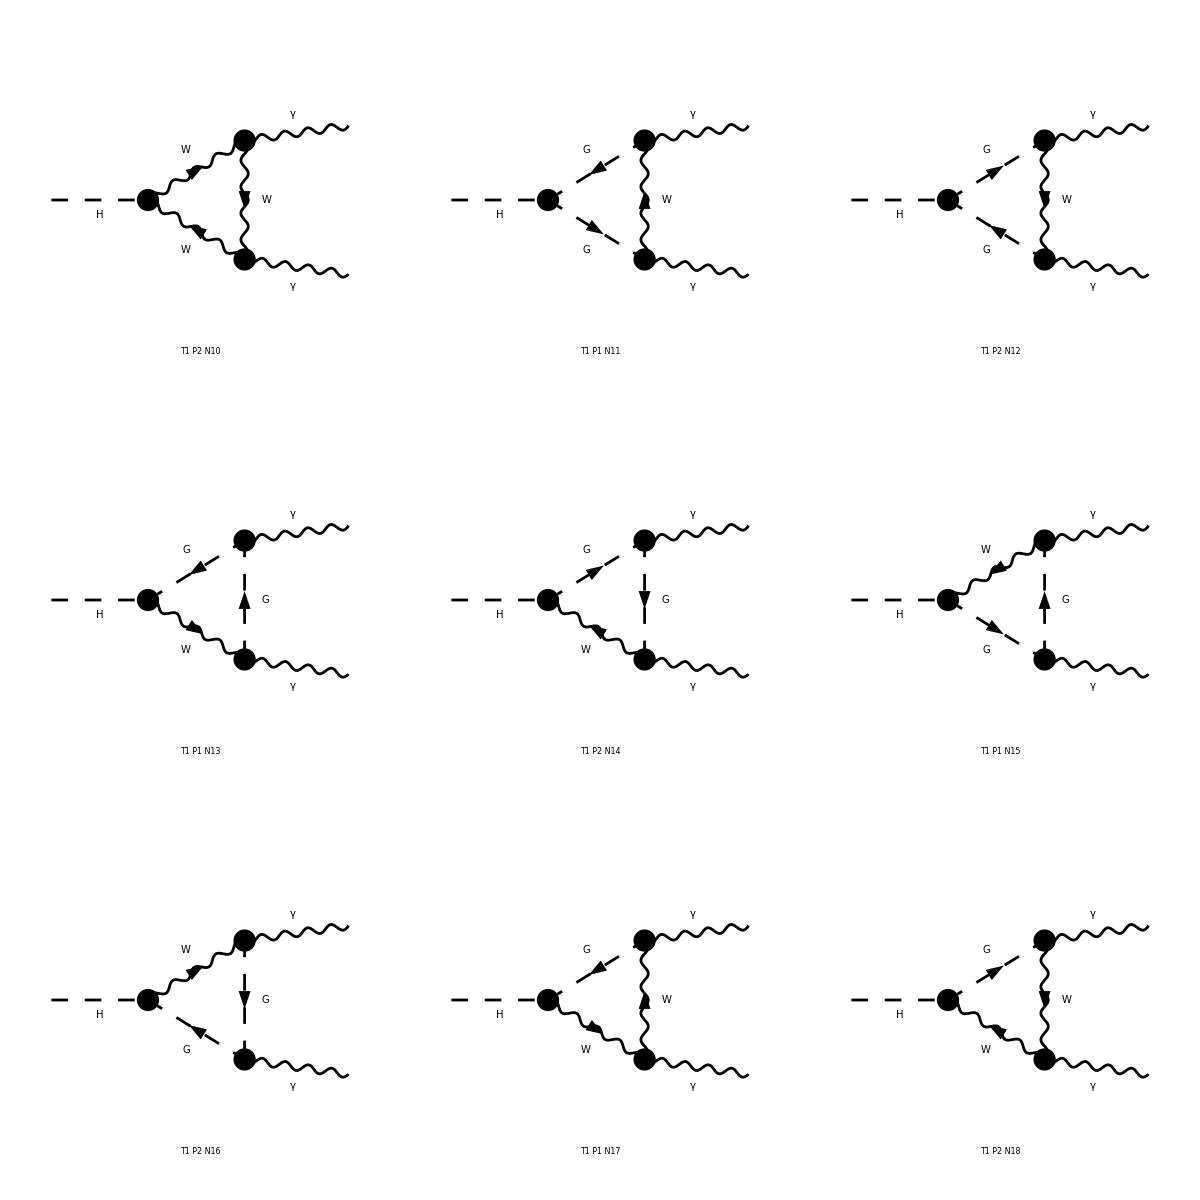

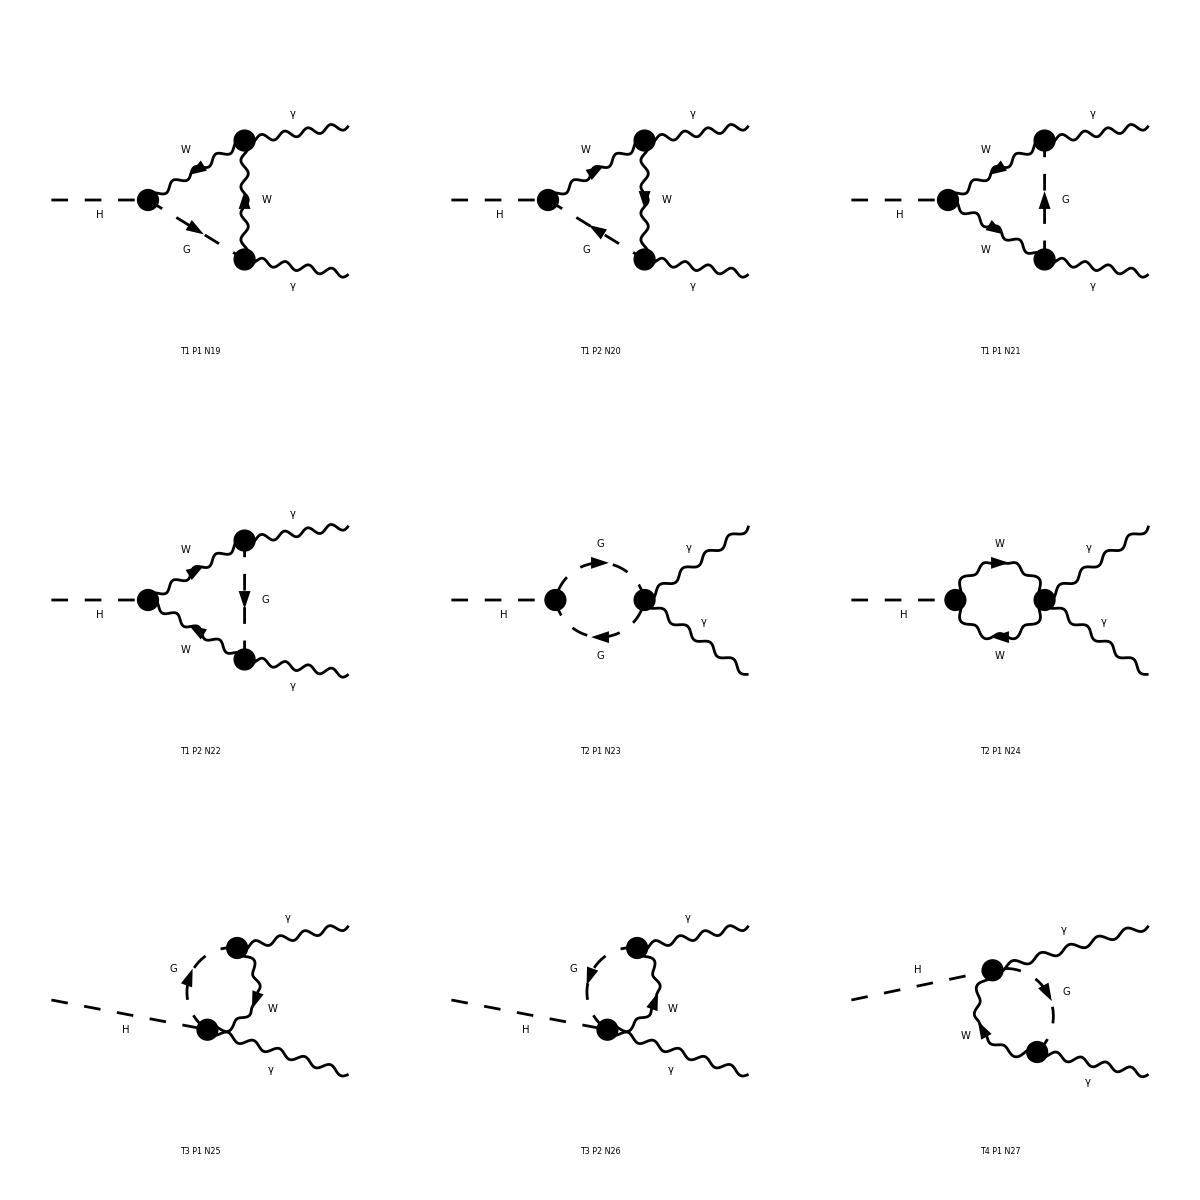

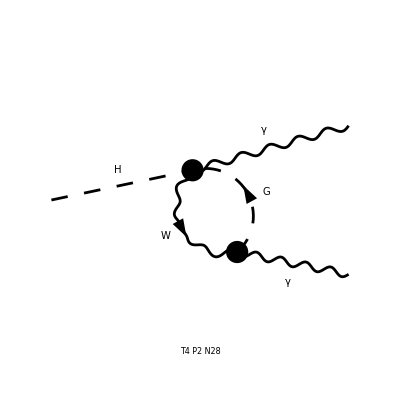

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
diag1=InsertFields[topo1,{S[1]}->{V[1],V[1]},InsertionLevel->{Particles},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 22 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 28 Particles amplitudes

preparing FORM code in /Users/misho/Documents/website/phys/FeynLecture/all_20130720/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],MH,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][1/(π SW)Alfa EL (Pair1 ((4 MT2 B0i[bb0,0,MT2,MT2])/(3 MW)-1/4 Sub1 B0i[bb0,MH2,MW2,MW2])-(2 Abb3 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2])/(3 MW)-1/4 MW Sub2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]+Pair1 (-(16 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2])/(3 MW)+Sub1 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+1/4 MH2 MW C0i[cc1,0,0,MH2,MW2,MW2,MW2])-(4 Abb4 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2])/(3 MW)+1/2 Sub3 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+Pair2 Pair3 (-(16 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]+C0i[cc22,0,0,MH2,MT2,MT2,MT2]))/(3 MW)+Sub1 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]+C0i[cc22,0,0,MH2,MW2,MW2,MW2])))]

To configm this diagram converges...

```mathematica
UVDivergentPart[amp]
```

Amp[{{S[1],k[1],MH,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][(Alfa EL (Pair1 ((4 Divergence MT2)/(3 MW)-(Divergence Sub1)/4)+Pair1 (-(4 Divergence MT2)/(3 MW)+(Divergence Sub1)/4)))/(π SW)]

```mathematica
UVDivergentPart[amp//.Subexpr[]]//FullSimplify
```

Amp[{{S[1],k[1],MH,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][0]

PolarizationSum directory to the amplitude invokes SquaredME, HelicityME, and ColourME (with _Hel=0 option).

```mathematica
mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//Simplify
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/misho/Documents/website/phys/FeynLecture/all_20130720/fc-pol-1.frm

running FORM...

ok

1/(18 π SW2)Alfa Alfa2 (1/MW216 MT2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]+3 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+42 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) B0i[bb0,0,MT2,MT2]^*-1/MW23 (MH2+6 MW2) (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]+3 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+42 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) B0i[bb0,MH2,MW2,MW2]^*+16 MH2^2 MT2 ((4 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2])/MW2-12 C0i[cc0,0,0,MH2,MW2,MW2,MW2]+1/MW2(16 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]-3 (MH2+6 MW2) C0i[cc12,0,0,MH2,MW2,MW2,MW2]+16 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]-3 (MH2+6 MW2) C0i[cc2,0,0,MH2,MW2,MW2,MW2]+16 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]-3 (MH2+6 MW2) C0i[cc22,0,0,MH2,MW2,MW2,MW2])) C0i[cc0,0,0,MH2,MT2,MT2,MT2]^*+3 MH2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-64 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+195 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-4 (16 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]-3 (MH2+6 MW2) C0i[cc00,0,0,MH2,MW2,MW2,MW2])-MH2 (-3 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]+288 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]-54 (MH2+6 MW2) C0i[cc12,0,0,MH2,MW2,MW2,MW2]+272 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]-6 (9 MH2+55 MW2) C0i[cc2,0,0,MH2,MW2,MW2,MW2]+288 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]-54 (MH2+6 MW2) C0i[cc22,0,0,MH2,MW2,MW2,MW2])) C0i[cc0,0,0,MH2,MW2,MW2,MW2]^*-1/MW264 MT2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]+3 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+42 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc00,0,0,MH2,MT2,MT2,MT2]^*+1/MW212 (MH2+6 MW2) (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]+3 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+42 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-32 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+6 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+36 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc00,0,0,MH2,MW2,MW2,MW2]^*+3 MH2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]+3 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-4 (16 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]-3 (MH2+6 MW2) C0i[cc00,0,0,MH2,MW2,MW2,MW2])-MH2 (-3 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]+32 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]-6 (MH2+6 MW2) C0i[cc12,0,0,MH2,MW2,MW2,MW2]+16 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]-6 (MH2+7 MW2) C0i[cc2,0,0,MH2,MW2,MW2,MW2]+32 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]-6 (MH2+6 MW2) C0i[cc22,0,0,MH2,MW2,MW2,MW2])) C0i[cc1,0,0,MH2,MW2,MW2,MW2]^*-1/MW232 MH2 MT2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-8 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+27 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-48 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+78 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc12,0,0,MH2,MT2,MT2,MT2]^*+1/MW26 MH2 (MH2+6 MW2) (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-8 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+27 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-48 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+78 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc12,0,0,MH2,MW2,MW2,MW2]^*-1/MW216 MH2 MT2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-16 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+51 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-96 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+18 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+108 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-80 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+18 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+114 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-96 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+18 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+108 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc2,0,0,MH2,MT2,MT2,MT2]^*+6 MH2 ((16 MT2 (MH2+7 MW2) B0i[bb0,0,MT2,MT2])/MW2-(3 (MH2+6 MW2) (MH2+7 MW2) B0i[bb0,MH2,MW2,MW2])/MW2-MH2 ((8 MT2 (MH2+6 MW2) C0i[cc0,0,0,MH2,MT2,MT2,MT2])/MW2-3 (9 MH2+55 MW2) C0i[cc0,0,0,MH2,MW2,MW2,MW2])+(4 (MH2+7 MW2) (-16 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+3 (MH2+6 MW2) C0i[cc00,0,0,MH2,MW2,MW2,MW2]))/MW2-MH2 (-3 (MH2+7 MW2) C0i[cc1,0,0,MH2,MW2,MW2,MW2]+(32 MT2 (2 MH2+13 MW2) C0i[cc12,0,0,MH2,MT2,MT2,MT2])/MW2-(6 (MH2+6 MW2) (2 MH2+13 MW2) C0i[cc12,0,0,MH2,MW2,MW2,MW2])/MW2+(16 MT2 (3 MH2+19 MW2) C0i[cc2,0,0,MH2,MT2,MT2,MT2])/MW2-(6 (2 MH2^2+26 MH2 MW2+85 MW2^2) C0i[cc2,0,0,MH2,MW2,MW2,MW2])/MW2+(32 MT2 (2 MH2+13 MW2) C0i[cc22,0,0,MH2,MT2,MT2,MT2])/MW2-(6 (MH2+6 MW2) (2 MH2+13 MW2) C0i[cc22,0,0,MH2,MW2,MW2,MW2])/MW2)) C0i[cc2,0,0,MH2,MW2,MW2,MW2]^*-1/MW232 MH2 MT2 (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-8 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+27 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-48 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+78 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc22,0,0,MH2,MT2,MT2,MT2]^*+1/MW26 MH2 (MH2+6 MW2) (16 MT2 B0i[bb0,0,MT2,MT2]-3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2]-8 MH2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2]+27 MH2 MW2 C0i[cc0,0,0,MH2,MW2,MW2,MW2]-64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2]+12 MH2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+72 MW2 C0i[cc00,0,0,MH2,MW2,MW2,MW2]+3 MH2 MW2 C0i[cc1,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc12,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc12,0,0,MH2,MW2,MW2,MW2]-48 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]+78 MH2 MW2 C0i[cc2,0,0,MH2,MW2,MW2,MW2]-64 MH2 MT2 C0i[cc22,0,0,MH2,MT2,MT2,MT2]+12 MH2^2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]+72 MH2 MW2 C0i[cc22,0,0,MH2,MW2,MW2,MW2]) C0i[cc22,0,0,MH2,MW2,MW2,MW2]^*)

### Numerical Evaluation

```mathematica
Install["LoopTools"]
```

LinkObject[/Users/misho/Documents/Mathematica/lib/LoopTools-2.8/LoopTools,558,5]

```mathematica
VALUES[higgs_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,
MH->higgs,MH2->higgs^2}
MyResult[higgs_]:=mat//.VALUES[higgs]//Simplify
```

```mathematica
MyResult[125]
```

0.131154

### Compare to a literature

```mathematica
f[t_]:=If[t<1,-1/4(Log[(1+√(1-t))/(1-√(1-t))]-ⅈ π)^2,(ArcSin[√(1/t)])^2]
Fb[t_]:=2+3t+3t(2-t)f[t]
Ff[t_]:=-2t(1+(1-t)f[t])
Fs[t_]:=t(1-t f[t])
InSomePaper[higgs_]:=(Alfa MH2^2)/(8π SW2 MW2)Abs[Alfa*3*(2/3)^2 Ff[((2MT)/MH)^2]+Alfa*1*1^2 Fb[((2MW)/MH)^2]]^2//.VALUES[higgs]
```

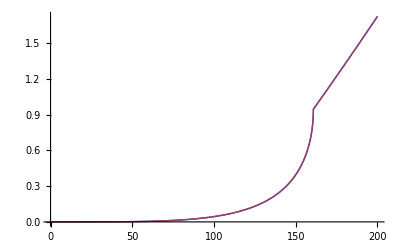

```mathematica
Plot[{MyResult[mh],InSomePaper[mh]},{mh,0,200}]
```

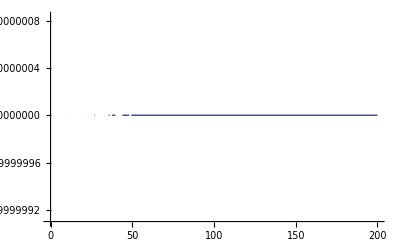

```mathematica
Plot[{MyResult[mh]/InSomePaper[mh]},{mh,0,200}]
```